```mathematica
(1-θ(1-θ)ν^2 Sin[Subscript[ξ, l]]^2)/(1+θ^2 ν^2 Sin[Subscript[ξ, l]]^2)/.θ->(m-1)/m
```

```mathematica
(m^2-(-1+m) ν^2 Sin[Subscript[ξ, l]]^2)/(m^2+(-1+m)^2 ν^2 Sin[Subscript[ξ, l]]^2)/.ν->0
```

1

```mathematica
D[(m^2-(-1+m) ν^2 Sin[Subscript[ξ, l]]^2)/(m^2+(-1+m)^2 ν^2 Sin[Subscript[ξ, l]]^2),ν]//Simplify
```

```mathematica
-(2 (-1+m) m^3 ν Sin[Subscript[ξ, l]]^2)/((m^2+(-1+m)^2 ν^2 Sin[Subscript[ξ, l]]^2)^2)//TeXForm
```

-\frac{2 (m-1) m^3 \nu  \sin ^2\left(\xi _l\right)}{\left((m-1)^2 \nu ^2 \sin ^2\left(\xi _l\right)+m^2\right){}^2}

```mathematica
-(2 (-1+m) m^3 ν Sin[Subscript[ξ, l]]^2)/((m^2+(-1+m)^2 ν^2 Sin[Subscript[ξ, l]]^2)^2)
```

```mathematica
-(2 θ ν Sin[Subscript[ξ, l]]^2)/((1+θ^2 ν^2 Sin[Subscript[ξ, l]]^2)^2)
```

```mathematica
With[{m=5},Table[(m^2-(-1+m) ν^2 Sin[(2π(l-1))/m]^2)/(m^2+(-1+m)^2 ν^2 Sin[(2π(l-1))/m]^2),{l,1,m}]]
```

{1,(25-4 (5/8+(√5)/8) ν^2)/(25+16 (5/8+(√5)/8) ν^2),(25-4 (5/8-(√5)/8) ν^2)/(25+16 (5/8-(√5)/8) ν^2),(25-4 (5/8-(√5)/8) ν^2)/(25+16 (5/8-(√5)/8) ν^2),(25-4 (5/8+(√5)/8) ν^2)/(25+16 (5/8+(√5)/8) ν^2)}

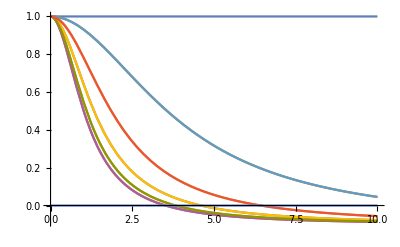

```mathematica
Plot[{Evaluate@With[{m=11},Table[(m^2-(-1+m) ν^2 Sin[(2π(l-1))/m]^2)/(m^2+(-1+m)^2 ν^2 Sin[(2π(l-1))/m]^2),{l,1,m}]],0},{ν,0,10},PlotRange->All]
```

```mathematica
With[{m=5,θ=1/2},Table[(1-θ(1-θ)ν^2 Sin[(2π(l-1))/m]^2)/(1+θ^2 ν^2 Sin[(2π(l-1))/m]^2),{l,1,m}]]
```

{1,(1-1/4 (5/8+(√5)/8) ν^2)/(1+1/4 (5/8+(√5)/8) ν^2),(1-1/4 (5/8-(√5)/8) ν^2)/(1+1/4 (5/8-(√5)/8) ν^2),(1-1/4 (5/8-(√5)/8) ν^2)/(1+1/4 (5/8-(√5)/8) ν^2),(1-1/4 (5/8+(√5)/8) ν^2)/(1+1/4 (5/8+(√5)/8) ν^2)}

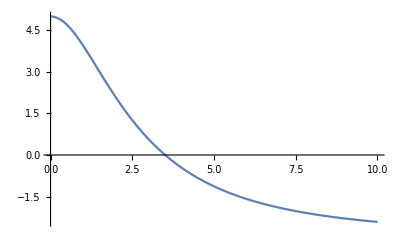

```mathematica
Plot[Total@{1,(1-1/4 (5/8+(√5)/8) ν^2)/(1+1/4 (5/8+(√5)/8) ν^2),(1-1/4 (5/8-(√5)/8) ν^2)/(1+1/4 (5/8-(√5)/8) ν^2),(1-1/4 (5/8-(√5)/8) ν^2)/(1+1/4 (5/8-(√5)/8) ν^2),(1-1/4 (5/8+(√5)/8) ν^2)/(1+1/4 (5/8+(√5)/8) ν^2)},{ν,0,10},PlotRange->All]
```

```mathematica
Sum[-Cos[(j-1)(2π(l-1))/m],{l,2,m}]
```

```mathematica
-1/2 Csc[((-1+j) π)/m] (2 Sin[(π-j π)/m])
```

```mathematica
-Csc[((-1+j) π)/m] Sin[(π-j π)/m]
```

```mathematica
1
```

```mathematica
With[{m=5},A=DiagonalMatrix[ConstantArray[-1/2,m-1],-1,m]+DiagonalMatrix[ConstantArray[1/2,m-1],1,m];A[[1,m]] = -1/2;A[[m,1]] = 1/2;A//Eigenvalues]
```

```mathematica
{1/2 ⅈ √(1/2 (5+√5)),-1/2 ⅈ √(1/2 (5+√5)),1/2 ⅈ √(1/2 (5-√5)),-1/2 ⅈ √(1/2 (5-√5)),0}//N
```

{0.+0.951057 ⅈ,0.-0.951057 ⅈ,0.+0.587785 ⅈ,0.-0.587785 ⅈ,0.}

```mathematica
-1/2 Exp[(2π I)/m(l-1)]+1/2 Exp[(2π I)/m(m-1)(l-1)]
```

```mathematica
With[{m=5},Table[+ⅈ (Cos[(-1+l) π] Sin[-π+l π+(2 π)/m-(2 l π)/m]),{l,1,m}]]//N
```

{0.,0.-0.951057 ⅈ,0.-0.587785 ⅈ,0.+0.587785 ⅈ,0.+0.951057 ⅈ}

```mathematica
+ⅈ (Cos[(-1+l) π] Sin[-π+l π+(2 π)/m-(2 l π)/m])
```

```mathematica
-ⅈ Cos[(-1+l) π] Sin[l π+-(2 (-1+l) π)/m]
```

```mathematica
ⅈ Cos[(-1+l) π] Sin[-l π+(2 (-1+l) π)/m]
```

```mathematica
ⅈ Cos[(-1+l) π] (Sin[-l π+(2 (-1+l) π)/m])
```

```mathematica
ⅈ Cos[(-1+l) π] (Cos[l π] Sin[(2 (-1+l) π)/m]-Cos[(2 (-1+l) π)/m] Sin[l π])
```

```mathematica
ⅈ Cos[(-1+l) π] (+Cos[l π] Sin[(2 (-1+l) π)/m])
```

```mathematica
Sin[(2 (-1+l) π)/m]==-Sin[(2 (-1+k) π)/m]
```

```mathematica
2 Cos[((k-l) π)/m] Sin[((-2+k+l) π)/m]
```

```mathematica
Solve[-2+k+l==0,k]
```

{{k→2-l}}

```mathematica
Sin[(2 (-1+l) π)/m]/.l->2
```

Sin[(2 π)/m]

```mathematica
With[{m=6},Table[- Sin[(2 (-1+l) π)/m],{l,1,m}]]
```

{0,-(√3)/2,-(√3)/2,0,(√3)/2,(√3)/2}

```mathematica
With[{m=6},Table[Sin[(2 (-1+m-l-1) π)/m],{l,1,m}]]
```

{0,(√3)/2,(√3)/2,0,-(√3)/2,-(√3)/2}

```mathematica
%296==%297
```

True

```mathematica
-Sin[(2 (-1+l) π)/m]==Sin[2 π-(4 π)/m-(2 l π)/m]
```

```mathematica
-Sin[-(2 π)/m+(2 l π)/m]==Sin[2 π-(2 l π)/m]
```

Sin[(2 π)/m-(2 l π)/m]==-Sin[(2 l π)/m]

```mathematica
-Sin[(2 (-1+l) π)/m]==Sin[2 π-(2 π)/m-(2 l π)/m]
```

```mathematica
-Sin[-(2 π)/m+(2 l π)/m]==-Sin[(2 π)/m+(2 l π)/m]
```

```mathematica
Cos[β] Sin[α]-Cos[α] Sin[β]
```

```mathematica
-Sin[(2 (-1+l) π)/m]+Cos[l π] Sin[((2+l (-2+m)) π)/m]/.l->2k
```

```mathematica
-2 Cos[k π] Sin[-((2+k (-4+m)) π)/m]
```

```mathematica
Table[ I Sin[(2π(l-1))/5],{l,1,5}]//N//RotateLeft
```

{0.+0.951057 ⅈ,0.+0.587785 ⅈ,0.-0.587785 ⅈ,0.-0.951057 ⅈ,0.}

```mathematica
Table[-1/2 Exp[(2π I)/5]^(l-1)+1/2 Exp[(2π I)/5]^(4(l-1)),{l,1,5}]//N
```

{0.,0.-0.951057 ⅈ,0.-0.587785 ⅈ,0.+0.587785 ⅈ,0.+0.951057 ⅈ}

```mathematica
1/2 (-1+ⅇ^((4 ⅈ (-1+l) π)/m))/.m->5/.l->2.
```

-0.345492+0.475528 ⅈ

```mathematica
-5/8-(√5)/8+1/2 ⅈ √(5/8-(√5)/8)//N
```

-0.904508+0.293893 ⅈ

```mathematica
I Sin[(2π(l-1))/m]
```

```mathematica
π==(2π(l-1))/m/.m->2k
```

π==((-1+l) π)/k

```mathematica
Reduce[π==((-1+l) π)/k&&1≤l≤2k&&k>0,l]
```

k≥1&&l==1+k

```mathematica
(-θ(1-θ))/(+θ^2)
```

-(1-θ)/θ

```mathematica
Limit[(1-θ(1-θ)ν^2 Sin[Subscript[ξ, l]]^2)/(1+θ^2 ν^2 Sin[Subscript[ξ, l]]^2),ν->∞]//Apart
```

(-1+θ)/θ

```mathematica
Reduce[π M==(2π(l-1))/(2k+1)(j-1)&&2≤l≤2k+1&&k>0&&2≤j≤2k+1&&k∈Integers&&l∈Integers&&j∈Integers,l]
```

False

```mathematica
M(2k+1)==(2(l-1))/1(j-1)
```

(1+2 k) M==2 (-1+j) (-1+l)

```mathematica
Limit[((1-θ(1-θ)ν^2 Sin[Subscript[ξ, l]]^2)Cos[(j-1)Subscript[ξ, l]]-ν Sin[Subscript[ξ, l]]^2)/(1+θ^2 ν^2 Sin[Subscript[ξ, l]]^2),ν->∞]
```

```mathematica
(Csc[Subscript[ξ, l]]^2 (-θ Cos[(-1+j) Subscript[ξ, l]] Sin[Subscript[ξ, l]]^2+θ^2 Cos[(-1+j) Subscript[ξ, l]] Sin[Subscript[ξ, l]]^2))/θ^2//Simplify
```

((-1+θ) Cos[(-1+j) ξ_l])/θ

```mathematica
((1-θ(1-θ)ν^2 Sin[Subscript[ξ, l]]^2)Cos[(j-1)Subscript[ξ, l]]-ν Sin[Subscript[ξ, l]]^2)/(1+θ^2 ν^2 Sin[Subscript[ξ, l]]^2)/.j->m
```

(-ν Sin[ξ_l]^2+Cos[(-1+m) ξ_l] (1-(1-θ) θ ν^2 Sin[ξ_l]^2))/(1+θ^2 ν^2 Sin[ξ_l]^2)

```mathematica
Cos[(-1+m) Subscript[ξ, l]]==Cos[ Subscript[ξ, l]]
```

```mathematica
Cos[(-1+m)(2π(l-1))/m]==Cos[Subscript[ξ, l]]
```

```mathematica
Cos[(2 (-1+l) π)/m]==Cos[Subscript[ξ, l]]
```

```mathematica
(1+(1-θ)ν I Sin[(2π(l-1))/m])/(1-θ ν I Sin[(2π(l-1))/m])Exp[- I(j-1)(2π(l-1))/m]
```

```mathematica
((Cos[Exp[- I(j-1)(2π(l-1))/m]]+I Sin[Exp[- I(j-1)(2π(l-1))/m]]) (1+ⅈ (1-θ) ν Sin[(2 (-1+l) π)/m])(1+ⅈ θ ν Sin[(2 (-1+l) π)/m]))/((1-ⅈ θ ν Sin[(2 (-1+l) π)/m])(1+ⅈ θ ν Sin[(2 (-1+l) π)/m]))
```

```mathematica
((Cos[- (j-1)(2π(l-1))/m]+I Sin[- (j-1)(2π(l-1))/m]) (1+ⅈ (1-θ) ν Sin[(2 (-1+l) π)/m])(1+ⅈ θ ν Sin[(2 (-1+l) π)/m]))/(1+θ^2 ν^2 Sin[(2 (-1+l) π)/m]^2)
```

```mathematica
1/(1+θ^2 ν^2 Sin[(2 (-1+l) π)/m]^2)(Cos[(2 (1-j) (-1+l) π)/m]+ⅈ ν Cos[(2 (1-j) (-1+l) π)/m] Sin[(2 (-1+l) π)/m]-θ ν^2 Cos[(2 (1-j) (-1+l) π)/m] Sin[(2 (-1+l) π)/m]^2+θ^2 ν^2 Cos[(2 (1-j) (-1+l) π)/m] Sin[(2 (-1+l) π)/m]^2+ⅈ Sin[(2 (1-j) (-1+l) π)/m]-ν Sin[(2 (-1+l) π)/m] Sin[(2 (1-j) (-1+l) π)/m]-ⅈ θ ν^2 Sin[(2 (-1+l) π)/m]^2 Sin[(2 (1-j) (-1+l) π)/m]+ⅈ θ^2 ν^2 Sin[(2 (-1+l) π)/m]^2 Sin[(2 (1-j) (-1+l) π)/m])
```

```mathematica
(Cos[(2 (1-j) (-1+l) π)/m]-θ ν^2 Cos[(2 (1-j) (-1+l) π)/m] Sin[(2 (-1+l) π)/m]^2+θ^2 ν^2 Cos[(2 (1-j) (-1+l) π)/m] Sin[(2 (-1+l) π)/m]^2-ν Sin[(2 (-1+l) π)/m] Sin[(2 (1-j) (-1+l) π)/m])
```

```mathematica
Cos[(2 (1-j) (-1+l) π)/m] (1-θ ν^2 Sin[(2 (-1+l) π)/m]^2+θ^2 ν^2 Sin[(2 (-1+l) π)/m]^2)-ν Sin[(2 (-1+l) π)/m] Sin[(2 (1-j) (-1+l) π)/m]
```

```mathematica
Cos[(2 (j-1) (-1+l) π)/m] (1-(1-θ) θ ν^2 Sin[(2 (-1+l) π)/m]^2)+ν Sin[(2 (-1+l) π)/m] Sin[(2 (j-1) (-1+l) π)/m]
```

```mathematica
(Cos[(2 (-1+j) (-1+l) π)/m] (1+(-1+θ) θ ν^2 Sin[(2 (-1+l) π)/m]^2)+ν Sin[(2 (-1+l) π)/m] Sin[(2 (-1+j) (-1+l) π)/m])/(1+θ^2 ν^2 Sin[(2 (-1+l) π)/m]^2)+ⅈ ((ν Cos[(2 (-1+j) (-1+l) π)/m] Sin[(2 (-1+l) π)/m]+(-1-(-1+θ) θ ν^2 Sin[(2 (-1+l) π)/m]^2) Sin[(2 (-1+j) (-1+l) π)/m])/(1+θ^2 ν^2 Sin[(2 (-1+l) π)/m]^2))
```

```mathematica
Cos[(2 (-1+j) (-1+l) π)/m]==Cos[(2  (-1+l) π)/m]/.j->m
```

```mathematica
2 Sin[-((-1+l) (-2+m) π)/m] Sin[(-1+l) π]
```

```mathematica
Sin[(2 (-1+j) (-1+l) π)/m]+Sin[(2  (-1+l) π)/m]/.j->m
```

```mathematica
2 Cos[-((-1+l) (-2+m) π)/m] Sin[(-1+l) π]
```

```mathematica
Assuming[m∈Integers&&m≥3&&j∈Integers&&1≤j≤m&&ν>0&&θ>0,1/m Sum[(1+(1-θ)ν I Sin[(2π(k-1))/m])/(1-θ ν I Sin[(2π(k-1))/m])Exp[- I(j-1)(2π(k-1))/m],{k,1,m}]]
```

(∑_(k=1)^m (ⅇ^(-(2 ⅈ (-1+j) (-1+k) π)/m) (1+ⅈ (1-θ) ν Sin[(2 (-1+k) π)/m]))/(1-ⅈ θ ν Sin[(2 (-1+k) π)/m]))/m

```mathematica
{Simplify@With[{m=6},Table[1/m Sum[(1+(1-θ)ν I Sin[(2π(l-1))/m])/(1-θ ν I Sin[(2π(l-1))/m])Exp[- I(j-1)(2π(l-1))/m],{l,1,m}],{j,1,m}]],With[{m=6},A=DiagonalMatrix[ConstantArray[-1/2,m-1],-1,m]+DiagonalMatrix[ConstantArray[1/2,m-1],1,m];A[[1,m]] = -1/2;A[[m,1]] = 1/2;(Inverse[IdentityMatrix[Length[A]]-θ ν A].(IdentityMatrix[Length[A]]+(1-θ) ν A))[[1]]//Simplify]}
```

{{(4-2 θ ν^2+3 θ^2 ν^2)/(4+3 θ^2 ν^2),(2 ν)/(4+3 θ^2 ν^2),(θ ν^2)/(4+3 θ^2 ν^2),0,(θ ν^2)/(4+3 θ^2 ν^2),-(2 ν)/(4+3 θ^2 ν^2)},{(4-2 θ ν^2+3 θ^2 ν^2)/(4+3 θ^2 ν^2),(2 ν)/(4+3 θ^2 ν^2),(θ ν^2)/(4+3 θ^2 ν^2),0,(θ ν^2)/(4+3 θ^2 ν^2),-(2 ν)/(4+3 θ^2 ν^2)}}

```mathematica
With[{m=5},A=DiagonalMatrix[ConstantArray[-1/2,m-1],-1,m]+DiagonalMatrix[ConstantArray[1/2,m-1],1,m];A[[1,m]] = -1/2;A[[m,1]] = 1/2;(Inverse[IdentityMatrix[Length[A]]-θ ν A].(IdentityMatrix[Length[A]]+(1-θ) ν A))[[1]]//Simplify]
```

{(16-8 θ ν^2+20 θ^2 ν^2-4 θ^3 ν^4+5 θ^4 ν^4)/(16+20 θ^2 ν^2+5 θ^4 ν^4),(ν (8+4 θ^2 ν^2+θ^3 ν^3))/(16+20 θ^2 ν^2+5 θ^4 ν^4),(θ ν^2 (4-2 θ ν+θ^2 ν^2))/(16+20 θ^2 ν^2+5 θ^4 ν^4),(θ ν^2 (4+2 θ ν+θ^2 ν^2))/(16+20 θ^2 ν^2+5 θ^4 ν^4),(ν (-8-4 θ^2 ν^2+θ^3 ν^3))/(16+20 θ^2 ν^2+5 θ^4 ν^4)}

```mathematica
%236==%235//Simplify
```

True

```mathematica
FullSimplify[(ν (32+32 θ^2 ν^2+6 θ^4 ν^4-θ^5 ν^5))/(16 (1+θ^2 ν^2 Cos[π/14]^2) (2+θ^2 ν^2 (1+Sin[π/14])) (-2+θ^2 ν^2 (-1+Sin[(3 π)/14])))==(ν (-32-32 θ^2 ν^2-6 θ^4 ν^4+θ^5 ν^5))/(64+112 θ^2 ν^2+56 θ^4 ν^4+7 θ^6 ν^6),θ>0&&ν>0]
```

True

```mathematica
(ν (-32-32 θ^2 ν^2-6 θ^4 ν^4+θ^5 ν^5))/(64+112 θ^2 ν^2+56 θ^4 ν^4+7 θ^6 ν^6)
```

```mathematica
16 (1+θ^2 ν^2 Cos[π/14]^2) (2+θ^2 ν^2 (1+Sin[π/14])) (-2+θ^2 ν^2 (-1+Sin[(3 π)/14]))//Expand
```

```mathematica
-64-112 θ^2 ν^2-56 θ^4 ν^4-7 θ^6 ν^6==-(64+112 θ^2 ν^2+56 θ^4 ν^4+7 θ^6 ν^6)
```

True

### To show the negativity of the top right element:

```mathematica
(1+(1-θ)ν I Sin[(2π(l-1))/m])/(1-θ ν I Sin[(2π(l-1))/m])Exp[- I(j-1)(2π(l-1))/m]/.j->m
```

(ⅇ^(-(2 ⅈ (-1+l) (-1+m) π)/m) (1+ⅈ (1-θ) ν Sin[(2 (-1+l) π)/m]))/(1-ⅈ θ ν Sin[(2 (-1+l) π)/m])

We use this identity:

```mathematica
FullSimplify[Exp[- I(m-1)(2π(l-1))/m]==Exp[I(2π(l-1))/m],l∈Integers&&m∈Integers]
```

True

```mathematica
(Exp[I(2π(l-1))/m] (1+ⅈ (1-θ) ν Sin[(2 (-1+l) π)/m]))/(1-ⅈ θ ν Sin[(2 (-1+l) π)/m])
```

(ⅇ^((2 ⅈ (-1+l) π)/m) (1+ⅈ (1-θ) ν Sin[(2 (-1+l) π)/m]))/(1-ⅈ θ ν Sin[(2 (-1+l) π)/m])

And multiply with the complex conjugate:

```mathematica
(Exp[I(2π(l-1))/m] (1+ⅈ (1-θ) ν Sin[(2 (-1+l) π)/m])(1+ⅈ θ ν Sin[(2 (-1+l) π)/m]))/((1-ⅈ θ ν Sin[(2 (-1+l) π)/m])(1+ⅈ θ ν Sin[(2 (-1+l) π)/m]))
```

```mathematica
(Exp[I(2π(l-1))/m] (1+ⅈ (1-θ) ν Sin[(2 (-1+l) π)/m])(1+ⅈ θ ν Sin[(2 (-1+l) π)/m]))/(1+θ^2 ν^2 Sin[(2 (-1+l) π)/m]^2)
```

```mathematica
1/(1+θ^2 ν^2 Sin[(2 (-1+l) π)/m]^2)(-ν Sin[(2 (-1+l) π)/m]^2+Cos[(2 (-1+l) π)/m] (1+(-1+θ) θ ν^2 Sin[(2 (-1+l) π)/m]^2)+ⅈ (Sin[(2 (-1+l) π)/m] (1+ν Cos[(2 (-1+l) π)/m]+(-1+θ) θ ν^2 Sin[(2 (-1+l) π)/m]^2)))
```

```mathematica
With[{m=1},Sum[Sin[(2 (-1+l) π)/m]/(1+θ^2 ν^2 Sin[(2 (-1+l) π)/m]^2) (1+ν Cos[(2 (-1+l) π)/m]+(-1+θ) θ ν^2 Sin[(2 (-1+l) π)/m]^2),{l,1,m}]]
```

0

```mathematica
Simplify[Sum[Sin[(2 (-1+l) π)/m]/(1+θ^2 ν^2 Sin[(2 (-1+l) π)/m]^2) (1+ν Cos[(2 (-1+l) π)/m]+(-1+θ) θ ν^2 Sin[(2 (-1+l) π)/m]^2),{l,1,m}],m∈Integers&&m>0]
```

$Aborted

```mathematica
With[{m=5},Sum[sin[(2 (-1+l) π)/m]/(1+θ^2 ν^2 Sin[(2 (-1+l) π)/m]^2) (1+ν Cos[(2 (-1+l) π)/m]+(-1+θ) θ ν^2 Sin[(2 (-1+l) π)/m]^2),{l,1,m}]]
```

```mathematica
Sin[(2 (-1+l) π)/m] (1+ν Cos[(2 (-1+l) π)/m]+(-1+θ) θ ν^2 Sin[(2 (-1+l) π)/m]^2)
```

```mathematica
With[{m=7},Sum[Sin[(2 (-1+l) π)/m]/(1+θ^2 ν^2 Sin[(2 (-1+l) π)/m]^2) (0(1+ν Cos[(2 (-1+l) π)/m])+(-1+θ) θ ν^2 Sin[(2 (-1+l) π)/m]^2),{l,1,m}]]
```

0

### To directly show that the imaginary parts is 0, it is enough to prove separately that

```mathematica
With[{m=5},{Sum[sin[(2 (-1+l) π)/m]/(1+θ^2 ν^2 Sin[(2 (-1+l) π)/m]^2) ,{l,1,m,2}],Sum[(sin[(2 (-1+l) π)/m] Cos[(2 (-1+l) π)/m])/(1+θ^2 ν^2 Sin[(2 (-1+l) π)/m]^2) ,{l,1,m,2}],Sum[sin[(2 (-1+l) π)/m]^3/(1+θ^2 ν^2 Sin[(2 (-1+l) π)/m]^2) ,{l,1,m,2}]}]
```

{sin[0]+sin[(4 π)/5]/(1+(5/8-(√5)/8) θ^2 ν^2)+sin[(8 π)/5]/(1+(5/8+(√5)/8) θ^2 ν^2),sin[0]+((-1-√5) sin[(4 π)/5])/(4 (1+(5/8-(√5)/8) θ^2 ν^2))+((-1+√5) sin[(8 π)/5])/(4 (1+(5/8+(√5)/8) θ^2 ν^2)),sin[0]^3+sin[(4 π)/5]^3/(1+(5/8-(√5)/8) θ^2 ν^2)+sin[(8 π)/5]^3/(1+(5/8+(√5)/8) θ^2 ν^2)}

```mathematica
With[{m=5},{Sum[sin[(2 (-1+l) π)/m]/(1+θ^2 ν^2 Sin[(2 (-1+l) π)/m]^2) ,{l,2,m,2}],Sum[(sin[(2 (-1+l) π)/m] Cos[(2 (-1+l) π)/m])/(1+θ^2 ν^2 Sin[(2 (-1+l) π)/m]^2) ,{l,2,m,2}],Sum[sin[(2 (-1+l) π)/m]^3/(1+θ^2 ν^2 Sin[(2 (-1+l) π)/m]^2) ,{l,2,m,2}]}]
```

{sin[(2 π)/5]/(1+(5/8+(√5)/8) θ^2 ν^2)+sin[(6 π)/5]/(1+(5/8-(√5)/8) θ^2 ν^2),((-1+√5) sin[(2 π)/5])/(4 (1+(5/8+(√5)/8) θ^2 ν^2))+((-1-√5) sin[(6 π)/5])/(4 (1+(5/8-(√5)/8) θ^2 ν^2)),sin[(2 π)/5]^3/(1+(5/8+(√5)/8) θ^2 ν^2)+sin[(6 π)/5]^3/(1+(5/8-(√5)/8) θ^2 ν^2)}

```mathematica
sin[(8 π)/5]==-sin[(2 π)/5]/.sin->Sin
```

True

### And this is true, since every term has a corresponding negative term.

### If m=2k, the terms with the cos drop out due to the identity:

```mathematica
With[{m=16},Table[Cos[(2 (-1+l) π)/m],{l,1,m}]]
```

{1,Cos[π/8],1/(√2),Sin[π/8],0,-Sin[π/8],-1/(√2),-Cos[π/8],-1,-Cos[π/8],-1/(√2),-Sin[π/8],0,Sin[π/8],1/(√2),Cos[π/8]}

1≤l≤k

```mathematica
Cos[(2 (-1+l) π)/(2k)]==-Cos[(2 (-1+l+k) π)/(2k)]
```

```mathematica
Cos[-π/k+(l π)/k]==-Cos[π-π/k+(l π)/k]//Simplify
```

True

### To show that M_(1,2)=-M_(1,m) for m=2k≥4:

j=2:

```mathematica
(1+(1-θ)ν I Sin[(2π(l-1))/m])/(1-θ ν I Sin[(2π(l-1))/m])Exp[- I(2-1)(2π(l-1))/m]
```

```mathematica
(1+(1-θ)ν I Sin[(2π(l-1))/m])/(1-θ ν I Sin[(2π(l-1))/m])Exp[- I(2π(l-1))/m]
```

```mathematica
With[{m=6},Table[(1+(1-θ)ν I Sin[(2π(l-1))/m])/(1-θ ν I Sin[(2π(l-1))/m])Exp[- I(2π(l-1))/m],{l,1,m}]]
```

```mathematica
{1,(ⅇ^(-(ⅈ π)/3) (1+1/2 ⅈ √3 (1-θ) ν))/(1-1/2 ⅈ √3 θ ν),(ⅇ^(-(2 ⅈ π)/3) (1+1/2 ⅈ √3 (1-θ) ν))/(1-1/2 ⅈ √3 θ ν),-1,(ⅇ^((2 ⅈ π)/3) (1-1/2 ⅈ √3 (1-θ) ν))/(1+1/2 ⅈ √3 θ ν),(ⅇ^((ⅈ π)/3) (1-1/2 ⅈ √3 (1-θ) ν))/(1+1/2 ⅈ √3 θ ν)}//N
```

{1.,((0.5-0.866025 ⅈ) (1.+(0.+0.866025 ⅈ) (1.-1. θ) ν))/(1.-(0.+0.866025 ⅈ) θ ν),-((0.5+0.866025 ⅈ) (1.+(0.+0.866025 ⅈ) (1.-1. θ) ν))/(1.-(0.+0.866025 ⅈ) θ ν),-1.,-((0.5-0.866025 ⅈ) (1.-(0.+0.866025 ⅈ) (1.-1. θ) ν))/(1.+(0.+0.866025 ⅈ) θ ν),((0.5+0.866025 ⅈ) (1.-(0.+0.866025 ⅈ) (1.-1. θ) ν))/(1.+(0.+0.866025 ⅈ) θ ν)}

j=m:

```mathematica
(1+(1-θ)ν I Sin[(2π(l-1))/m])/(1-θ ν I Sin[(2π(l-1))/m])Exp[- I(j-1)(2π(l-1))/m]/.j->m
```

```mathematica
(1+(1-θ)ν I Sin[(2π(l-1))/m])/(1-θ ν I Sin[(2π(l-1))/m])Exp[- I(m-1)(2π(l-1))/m]
```

```mathematica
(1+(1-θ)ν I Sin[(2π(l-1))/m])/(1-θ ν I Sin[(2π(l-1))/m])Exp[ I(2π(l-1))/m]
```

```mathematica
{Sum[(1+(1-θ)ν I Sin[(2π(l-1))/m])/(1-θ ν I Sin[(2π(l-1))/m])exp[- I(2π(l-1))/m],{l,1,m}],Sum[(1+(1-θ)ν I Sin[(2π(l-1))/m])/(1-θ ν I Sin[(2π(l-1))/m])exp[ I(2π(l-1))/m],{l,1,m}]}
```

```mathematica
{∑_(l=1)^m (exp[-(2 ⅈ (-1+l) π)/m] (1+ⅈ (1-θ) ν Sin[(2 (-1+l) π)/m]))/(1-ⅈ θ ν Sin[(2 (-1+l) π)/m]),∑_(l=1)^m (exp[(2 ⅈ (-1+l) π)/m] (1+ⅈ (1-θ) ν Sin[(2 (-1+l) π)/m]))/(1-ⅈ θ ν Sin[(2 (-1+l) π)/m])}
```

```mathematica
{∑_(l=1)^m (exp[-(2 ⅈ (-1+l) π)/m] (1+ⅈ (1-θ) ν Sin[(2 (-1+l) π)/m])(1+ⅈ θ ν Sin[(2 (-1+l) π)/m]))/((1-ⅈ θ ν Sin[(2 (-1+l) π)/m])(1+ⅈ θ ν Sin[(2 (-1+l) π)/m])),∑_(l=1)^m (exp[(2 ⅈ (-1+l) π)/m] (1+ⅈ (1-θ) ν Sin[(2 (-1+l) π)/m])(1+ⅈ θ ν Sin[(2 (-1+l) π)/m]))/((1-ⅈ θ ν Sin[(2 (-1+l) π)/m])(1+ⅈ θ ν Sin[(2 (-1+l) π)/m]))}
```

```mathematica
{∑_(l=1)^m (Exp[-(2 ⅈ (-1+l) π)/m] (1+ⅈ (1-θ) ν Sin[(2 (-1+l) π)/m])(1+ⅈ θ ν Sin[(2 (-1+l) π)/m]))/(1+θ^2 ν^2 Sin[(2 (-1+l) π)/m]^2),∑_(l=1)^m (Exp[(2 ⅈ (-1+l) π)/m] (1+ⅈ (1-θ) ν Sin[(2 (-1+l) π)/m])(1+ⅈ θ ν Sin[(2 (-1+l) π)/m]))/(1+θ^2 ν^2 Sin[(2 (-1+l) π)/m]^2)}
```

```mathematica
{∑_(l=1)^m 1/(1+θ^2 ν^2 Sin[(2 (-1+l) π)/m]^2)((ν Sin[(2 (-1+l) π)/m]^2+Cos[(2 (-1+l) π)/m] (1+(-1+θ) θ ν^2 Sin[(2 (-1+l) π)/m]^2))+ⅈ (Sin[(2 (-1+l) π)/m] (-1+ν Cos[(2 (-1+l) π)/m]-(-1+θ) θ ν^2 Sin[(2 (-1+l) π)/m]^2))),∑_(l=1)^m 1/(1+θ^2 ν^2 Sin[(2 (-1+l) π)/m]^2)((-ν Sin[(2 (-1+l) π)/m]^2+Cos[(2 (-1+l) π)/m] (1+(-1+θ) θ ν^2 Sin[(2 (-1+l) π)/m]^2))+ⅈ (Sin[(2 (-1+l) π)/m] (1+ν Cos[(2 (-1+l) π)/m]+(-1+θ) θ ν^2 Sin[(2 (-1+l) π)/m]^2)))}
```

we can drop the imaginary parts (because they are 0):

```mathematica
With[{m=8},{∑_(l=1)^m 1/(1+θ^2 ν^2 Sin[(2 (-1+l) π)/m]^2)(ν Sin[(2 (-1+l) π)/m]^2+Cos[(2 (-1+l) π)/m] (1+(-1+θ) θ ν^2 Sin[(2 (-1+l) π)/m]^2))==-∑_(l=1)^m 1/(1+θ^2 ν^2 Sin[(2 (-1+l) π)/m]^2)(-ν Sin[(2 (-1+l) π)/m]^2+Cos[(2 (-1+l) π)/m] (1+(-1+θ) θ ν^2 Sin[(2 (-1+l) π)/m]^2))}]
```

```mathematica
{(2 ν)/(1+θ^2 ν^2)+(2 (ν/2-(1+1/2 (-1+θ) θ ν^2)/(√2)))/(1+(θ^2 ν^2)/2)+(2 (ν/2+(1+1/2 (-1+θ) θ ν^2)/(√2)))/(1+(θ^2 ν^2)/2)==(2 ν)/(1+θ^2 ν^2)-(2 (-ν/2-(1+1/2 (-1+θ) θ ν^2)/(√2)))/(1+(θ^2 ν^2)/2)-(2 (-ν/2+(1+1/2 (-1+θ) θ ν^2)/(√2)))/(1+(θ^2 ν^2)/2)}//Simplify
```

{True}

so, by dropping the sin terms, it is enough to prove

```mathematica
With[{m=8},{∑_(l=1)^m 1/(1+θ^2 ν^2 Sin[(2 (-1+l) π)/m]^2)(Cos[(2 (-1+l) π)/m] (1+(-1+θ) θ ν^2 Sin[(2 (-1+l) π)/m]^2)),∑_(l=1)^m 1/(1+θ^2 ν^2 Sin[(2 (-1+l) π)/m]^2)(-Cos[(2 (-1+l) π)/m] (1+(-1+θ) θ ν^2 Sin[(2 (-1+l) π)/m]^2))}]//Simplify
```

{0,0}

so they are separately 0. We just deal with the 1st one: internal symmetry

```mathematica
With[{m=10},Table[1/(1+θ^2 ν^2 Sin[(2 (-1+l) π)/m]^2)(Cos[(2 (-1+l) π)/m] (1+(-1+θ) θ ν^2 Sin[(2 (-1+l) π)/m]^2)),{l,1,m}]]
```

```mathematica
{1,((1+√5) (1+(5/8-(√5)/8) (-1+θ) θ ν^2))/(4 (1+(5/8-(√5)/8) θ^2 ν^2)),((-1+√5) (1+(5/8+(√5)/8) (-1+θ) θ ν^2))/(4 (1+(5/8+(√5)/8) θ^2 ν^2)),((1-√5) (1+(5/8+(√5)/8) (-1+θ) θ ν^2))/(4 (1+(5/8+(√5)/8) θ^2 ν^2)),((-1-√5) (1+(5/8-(√5)/8) (-1+θ) θ ν^2))/(4 (1+(5/8-(√5)/8) θ^2 ν^2)),-1,((-1-√5) (1+(5/8-(√5)/8) (-1+θ) θ ν^2))/(4 (1+(5/8-(√5)/8) θ^2 ν^2)),((1-√5) (1+(5/8+(√5)/8) (-1+θ) θ ν^2))/(4 (1+(5/8+(√5)/8) θ^2 ν^2)),((-1+√5) (1+(5/8+(√5)/8) (-1+θ) θ ν^2))/(4 (1+(5/8+(√5)/8) θ^2 ν^2)),((1+√5) (1+(5/8-(√5)/8) (-1+θ) θ ν^2))/(4 (1+(5/8-(√5)/8) θ^2 ν^2))}//Simplify
```

{1,-(2+2 √5-√5 θ ν^2+√5 θ^2 ν^2)/(-8+(-5+√5) θ^2 ν^2),(-2+2 √5-√5 θ ν^2+√5 θ^2 ν^2)/(8+(5+√5) θ^2 ν^2),(2-2 √5+√5 θ ν^2-√5 θ^2 ν^2)/(8+(5+√5) θ^2 ν^2),(2+2 √5-√5 θ ν^2+√5 θ^2 ν^2)/(-8+(-5+√5) θ^2 ν^2),-1,(2+2 √5-√5 θ ν^2+√5 θ^2 ν^2)/(-8+(-5+√5) θ^2 ν^2),(2-2 √5+√5 θ ν^2-√5 θ^2 ν^2)/(8+(5+√5) θ^2 ν^2),(-2+2 √5-√5 θ ν^2+√5 θ^2 ν^2)/(8+(5+√5) θ^2 ν^2),-(2+2 √5-√5 θ ν^2+√5 θ^2 ν^2)/(-8+(-5+√5) θ^2 ν^2)}

```mathematica
-(2+2 √5-√5 θ ν^2+√5 θ^2 ν^2)/(-8+(-5+√5) θ^2 ν^2)==-(2+2 √5-√5 θ ν^2+√5 θ^2 ν^2)/(-8+(-5+√5) θ^2 ν^2)//Simplify
```

True

For 1≤l≤k: the terms with index l and index k+l are pairwise equal

```mathematica
{1/(1+θ^2 ν^2 Sin[(2 (-1+l) π)/m]^2)(Cos[(2 (-1+l) π)/m] (1+(-1+θ) θ ν^2 Sin[(2 (-1+l) π)/m]^2))/.m->2k,-1/(1+θ^2 ν^2 Sin[(2 (-1+l) π)/m]^2)(Cos[(2 (-1+l) π)/m] (1+(-1+θ) θ ν^2 Sin[(2 (-1+l) π)/m]^2))/.m->2k/.l->k+l}
```

```mathematica
With[{k=7},Table[{(Cos[((-1+l) π)/k] (1+(-1+θ) θ ν^2 Sin[((-1+l) π)/k]^2))/(1+θ^2 ν^2 Sin[((-1+l) π)/k]^2)==-(Cos[((-1+k+l) π)/k] (1+(-1+θ) θ ν^2 Sin[((-1+k+l) π)/k]^2))/(1+θ^2 ν^2 Sin[((-1+k+l) π)/k]^2)},{l,1,k}]]//Simplify
```

{{True},{True},{True},{True},{True},{True},{True}}

```mathematica
Simplify[Sin[-π/k+(l π)/k]^2==Sin[π-π/k+(l π)/k]^2]
```

True

```mathematica
Sin[π+α]//TrigExpand
```

-Sin[α]

```mathematica
Simplify[Cos[-π/k+(l π)/k]==-Cos[π-π/k+(l π)/k]]
```

True

```mathematica
-Cos[π+α]//TrigExpand
```

Cos[α]

### The denominators

```mathematica
With[{m=5},{Product[1-√μ I Sin[(2π(l-1))/m],{l,1,m}],(((√(1+μ)+1)/2)^m-((√(1+μ)-1)/2)^m//Expand)}]
```

{(1-ⅈ √(5/8-(√5)/8) √μ) (1+ⅈ √(5/8-(√5)/8) √μ) (1-ⅈ √(5/8+(√5)/8) √μ) (1+ⅈ √(5/8+(√5)/8) √μ),1+(5 μ)/4+(5 μ^2)/16}

```mathematica
FullSimplify[With[{k=5},{Product[1-√μ I Sin[(2π(l-1))/(2k+1)],{l,1,2k+1}]==(((√(1+μ)+1)/2)^(2k+1)-((√(1+μ)-1)/2)^(2k+1)//Expand)}],μ>0]
```

{True}

```mathematica
det[k_]:=Product[1-x I sin[(2π(l-1))/(2k+1)],{l,1,2k+1}]
```

```mathematica
det[2]/.x->1
```

(1-ⅈ √(5/8-(√5)/8)) (1+ⅈ √(5/8-(√5)/8)) (1-ⅈ √(5/8+(√5)/8)) (1+ⅈ √(5/8+(√5)/8))

These are polynomial identities of degree 2k+4:

```mathematica
With[{k=1},{det[k+2],((1+x^2/2)det[k+1]-x^4/16 det[k])}/.x->-I/Sin[(2π)/7]]/.sin->Sin
```

{0,-1/16 Sec[(3 π)/14]^4 (1-1/2 √3 Sec[(3 π)/14]) (1+1/2 √3 Sec[(3 π)/14])+(1-√(5/8-(√5)/8) Sec[(3 π)/14]) (1+√(5/8-(√5)/8) Sec[(3 π)/14]) (1-√(5/8+(√5)/8) Sec[(3 π)/14]) (1+√(5/8+(√5)/8) Sec[(3 π)/14]) (1-1/2 Sec[(3 π)/14]^2)}

```mathematica
With[{k=1},{det[k+2],((1+x^2/2)det[k+1]-x^4/16 det[k])}]/.x->-I/Sin[(2π)/7]
```

{(1-Sec[(3 π)/14] sin[0]) (1-Sec[(3 π)/14] sin[(2 π)/7]) (1-Sec[(3 π)/14] sin[(4 π)/7]) (1-Sec[(3 π)/14] sin[(6 π)/7]) (1-Sec[(3 π)/14] sin[(8 π)/7]) (1-Sec[(3 π)/14] sin[(10 π)/7]) (1-Sec[(3 π)/14] sin[(12 π)/7]),-1/16 Sec[(3 π)/14]^4 (1-Sec[(3 π)/14] sin[0]) (1-Sec[(3 π)/14] sin[(2 π)/3]) (1-Sec[(3 π)/14] sin[(4 π)/3])+(1-1/2 Sec[(3 π)/14]^2) (1-Sec[(3 π)/14] sin[0]) (1-Sec[(3 π)/14] sin[(2 π)/5]) (1-Sec[(3 π)/14] sin[(4 π)/5]) (1-Sec[(3 π)/14] sin[(6 π)/5]) (1-Sec[(3 π)/14] sin[(8 π)/5])}

### For x=1: interesting identities about the roots of unity are created

```mathematica
-1/16 Sec[(3 π)/14]^4 (1-Sec[(3 π)/14] sin[0]) (1-Sec[(3 π)/14] sin[(2 π)/3]) (1-Sec[(3 π)/14] sin[(4 π)/3])+(1-1/2 Sec[(3 π)/14]^2) (1-Sec[(3 π)/14] sin[0]) (1-Sec[(3 π)/14] sin[(2 π)/5]) (1-Sec[(3 π)/14] sin[(4 π)/5]) (1-Sec[(3 π)/14] sin[(6 π)/5]) (1-Sec[(3 π)/14] sin[(8 π)/5])/.sin->Sin
```

```mathematica
-1/16 Sec[(3 π)/14]^4 (1-1/2 √3 Sec[(3 π)/14]) (1+1/2 √3 Sec[(3 π)/14])+(1-√(5/8-(√5)/8) Sec[(3 π)/14]) (1+√(5/8-(√5)/8) Sec[(3 π)/14]) (1-√(5/8+(√5)/8) Sec[(3 π)/14]) (1+√(5/8+(√5)/8) Sec[(3 π)/14]) (1-1/2 Sec[(3 π)/14]^2)//Expand
```

```mathematica
1-7/4 Sec[(3 π)/14]^2+7/8 Sec[(3 π)/14]^4-7/64 Sec[(3 π)/14]^6//FullSimplify
```

0